```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Problem 3*)

(* Kinetic and Potential Energies around mass 1 and mass 2 *)
T=(1/2) m (y1t^2+z1t^2 + y2t^2+z2t^2)
V=m g (z1 + z2);

(* Positions *)
y1=l1 Sin[θ1];     
y2=l1 Sin[θ1]+l2 Sin[θ2]; 
z1 = -l1 Cos[θ1]; 
z2= -l1 Cos[θ1] - l2 Cos[θ2]; 
y1t=D[y1,θ1] θ1t;
y2t=D[y2,θ1] θ1t+D[y2,θ2] θ2t;
z1t=D[z1,θ1] θ1t;
z2t=D[z2,θ1] θ1t+D[z2,θ2] θ2t;

(* Torque done by the damper at the origin *)
τ = c θ1t;

(* External forcing. Assumes a solution of y = Ye^ⅈωt, θ = Θe^ⅈωt, F = {-T0 e^ⅈωt, Τ0e^ⅈωt} (because the motor on pendulum 1 exerts a torque on pendulum 2 and a reaction torque on itself)  
and the e^ⅈωt drops out when calculating the particular solution *)
f = {{Τ0},{-Τ0}};
```

1/2 m (θ1t^2 l1^2 sin^2(θ1)+θ1t^2 l1^2 cos^2(θ1)+(θ1t l1 sin(θ1)+θ2t l2 sin(θ2))^2+(θ1t l1 cos(θ1)+θ2t l2 cos(θ2))^2)

```mathematica
T=Collect[T,{θ1t,θ2t},Simplify]
V=Simplify[V]
f
```

θ1t^2 l1^2 m+θ1t θ2t l1 l2 m cos(θ1-θ2)+1/2 θ2t^2 l2^2 m

-g m (2 l1 cos(θ1)+l2 cos(θ2))

(Τ0
-Τ0)

```mathematica
(*First E-L equation*)
L=T-V;
D[L,θ1t];
D[%,θ1] θ1t+D[%,θ2] θ2t+D[%,θ1t]θ1tt+D[%,θ2t] θ2tt ;
D[L,θ1];
eqn1=Simplify[%%-%]
```

l1 m (2 g sin(θ1)+2 θ1tt l1+θ2t^2 l2 sin(θ1-θ2)+θ2tt l2 cos(θ1-θ2))

```mathematica
(*Second E-L equation*)
D[L,θ2t];
D[%,θ1] θ1t+D[%,θ2] θ2t +D[%,θ1t]θ1tt+D[%,θ2t] θ2tt;
D[L,θ2];
eqn2=Simplify[%%-%]
```

l2 m (g sin(θ2)+θ1t^2 (-l1) sin(θ1-θ2)+θ1tt l1 cos(θ1-θ2)+θ2tt l2)

```mathematica
(*Linearize first E-L equation. Trigonometric simplifications*)
leqn1=(eqn1 + τ)/.{Sin[θ1]->θ1,Cos[θ1-θ2]->1,Sin[θ1-θ2]->θ1-θ2,Cos[θ2]->1};
Expand[%];
%/.{θ2t^2->0};
leqn1=Simplify[%]
```

c θ1t+2 g θ1 l1 m+l1 m (2 θ1tt l1+θ2tt l2)

```mathematica
(*Linearize second E-L equation. Trigonometric simplifications*)
leqn2=eqn2/.{Sin[θ1]->θ1,Cos[θ1-θ2]->1,Sin[θ1-θ2]->θ1-θ2,Cos[θ2]->1, Sin[θ2]->θ2};
Expand[%];
%/.{θ1t^2->0};
leqn2=Simplify[%]
```

l2 m (g θ2+θ1tt l1+θ2tt l2)

```mathematica
nleqn1=Collect[leqn1 +τ/. {θ1tt->s^2 θ1, θ2tt->s^2 θ2, θ1t-> s θ1},{θ1,θ2, θ3},Simplify]
nleqn2=Collect[leqn2 /. {θ1tt->s^2 θ1, θ2tt->s^2 θ2},{θ1,θ2,θ3},Simplify]
```

2 θ1 (s (c+l1^2 m s)+g l1 m)+θ2 l1 l2 m s^2

θ2 l2 m (g+l2 s^2)+θ1 l1 l2 m s^2

```mathematica
(* Create coefficient matrix *)
A = {{nleqn1[[1]]/.{θ1->1}, nleqn1[[2]]/.{θ2->1}},
{nleqn2[[1]]/.{θ1->1}, nleqn2[[2]]/.{θ2->1}}}
```

(2 (g l1 m+s (m s l1^2+c)) | l1 l2 m s^2
l1 l2 m s^2 | l2 m (l2 s^2+g))

```mathematica
(* Sub in parameters for easy viewing *)
A/. parameters
```

(2 (s (s+1)+981/100) | s^2
s^2 | s^2+981/100)

```mathematica
(* Characteristic Polynomial *)
cp=Collect[Det[A],s,Simplify]
```

2 c g l2 m s+2 c l2^2 m s^3+2 g^2 l1 l2 m^2+2 g l1 l2 m^2 s^2 (l1+l2)+l1^2 l2^2 m^2 s^4

```mathematica
(* Solve for eigenvalue *)
soln=Solve[cp==0,s];
```

```mathematica
s1=s/.soln⟦2⟧ ;
s2=s/.soln⟦4⟧;
```

```mathematica
(* Multiply Θ1 and Θ2 by e^ⅈωt to get θ1 and θ2 *)
θ1func = Simplify[(((Inverse[A].f ) Exp[s t] /. {s-> I wf}))[[1,1]]]
θ2func = Simplify[(((Inverse[A].f)Exp[s t]/. {s-> I wf}))[[2,1]]]
```

(Τ0 ⅇ^(ⅈ t wf) (g-wf^2 (l1+l2)))/(-2 g wf (l1 m wf (l1+l2)-ⅈ c)+l2 wf^3 (l1^2 m wf-2 ⅈ c)+2 g^2 l1 m)

(Τ0 ⅇ^(ⅈ t wf) (-2 g l1 m+wf (l1 m wf (2 l1+l2)-2 ⅈ c)))/(l2 m (-2 g wf (l1 m wf (l1+l2)-ⅈ c)+l2 wf^3 (l1^2 m wf-2 ⅈ c)+2 g^2 l1 m))

```mathematica
ComplexExpand[θ1func];
```

```mathematica
ComplexExpand[θ2func];
```

```mathematica
(* Particular solution = real parts of θ1 and θ2 *)
yp = {(l1^2 l2^2 m Τ0 Cos[t wf] wf^6)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)+(l1^3 l2 m Τ0 Cos[t wf] wf^6)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)-(2 c l2^2 Τ0 Sin[t wf] wf^5)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)-(2 c l1 l2 Τ0 Sin[t wf] wf^5)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)-(2 g l1^3 m Τ0 Cos[t wf] wf^4)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)-(2 g l1 l2^2 m Τ0 Cos[t wf] wf^4)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)-(5 g l1^2 l2 m Τ0 Cos[t wf] wf^4)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)+(2 c g l1 Τ0 Sin[t wf] wf^3)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)+(4 c g l2 Τ0 Sin[t wf] wf^3)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)+(4 g^2 l1^2 m Τ0 Cos[t wf] wf^2)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)+(4 g^2 l1 l2 m Τ0 Cos[t wf] wf^2)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)-(2 c g^2 Τ0 Sin[t wf] wf)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)-(2 g^3 l1 m Τ0 Cos[t wf])/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2),-(2 l1^4 m Τ0 Cos[t wf] wf^6)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)-(l1^3 l2 m Τ0 Cos[t wf] wf^6)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)+(2 c l1^2 Τ0 Sin[t wf] wf^5)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)+(2 c l1 l2 Τ0 Sin[t wf] wf^5)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)+(8 g l1^3 m Τ0 Cos[t wf] wf^4)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)+(2 g l1^2 l2 m Τ0 Cos[t wf] wf^4)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)+(4 g l1^4 m Τ0 Cos[t wf] wf^4)/(l2 ((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2))-(4 c^2 Τ0 Cos[t wf] wf^4)/(m ((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2))-(2 c g l1 Τ0 Sin[t wf] wf^3)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)-(6 g^2 l1^2 m Τ0 Cos[t wf] wf^2)/((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2)-(8 g^2 l1^3 m Τ0 Cos[t wf] wf^2)/(l2 ((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2))+(4 c^2 g Τ0 Cos[t wf] wf^2)/(l2 m ((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2))+(4 g^3 l1^2 m Τ0 Cos[t wf])/(l2 ((2 c g wf-2 c l2 wf^3)^2+(l1^2 l2 m wf^4-2 g l1 (l1+l2) m wf^2+2 g^2 l1 m)^2))};
```

```mathematica
Clear[Τ0,wf]
```

```mathematica
(* T0 = 1/15 at c=10,000. w = .855 rad/sec *)
```

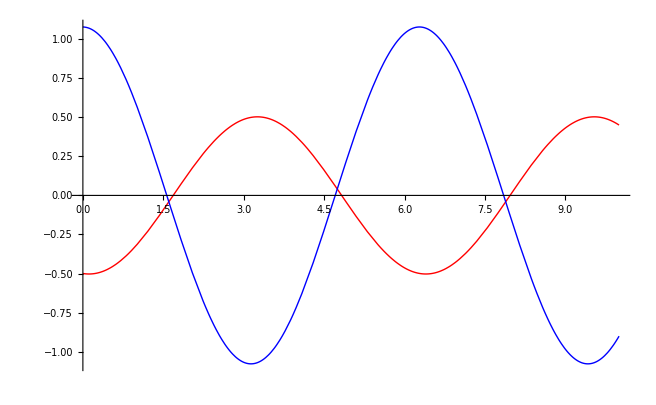

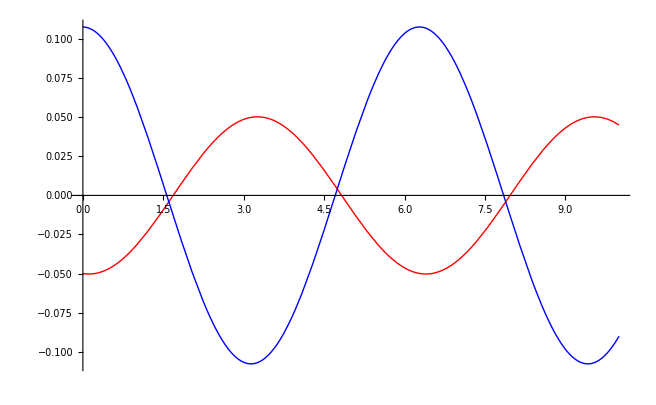

```mathematica
(* Red = pendulum 1 (with damping). Blue = pendulum 2. *)
(* High Τ0 -> big amplitude. Low F0 -> low amplitude *)
(* High wf -> Angular displacement decreases, out of phase. *)
(* Low wf -> Angular displacement decreases, out of phase. *)
(* High c -> pendulum 1 motion stops completely, pendulum 2 motion increased. Therefore, linearity DOES depend on the damping constant c, because the larger displacement get slightly bigger as c grows, up to a limit. The larger amplitude of the second pendulum does not change with high c, and it is therefore the limit. *)

(* High Τ0 vs. Low Τ0*)
parameters={m-> 1,l1->1,l2->1, g->981/100, Τ0->10, wf->1,c->1};
ypplot = yp /.parameters;
Plot[ypplot, {t,0,10}, PlotStyle->{Red, Blue}]

parameters={m-> 1,l1->1,l2->1, g->981/100, Τ0->1, wf->1,c->1};
ypplot = yp /.parameters;
Plot[ypplot, {t,0,10}, PlotStyle->{Red, Blue}]
```

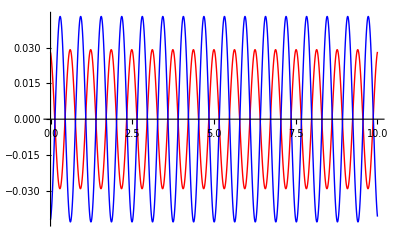

```mathematica
(* High wf *)
parameters={m-> 1,l1->1,l2->1, g->981/100, Τ0->1, wf->10,c->1};
ypplot = yp /.parameters;
Plot[ypplot, {t,0,10}, PlotStyle->{Red, Blue}]
```

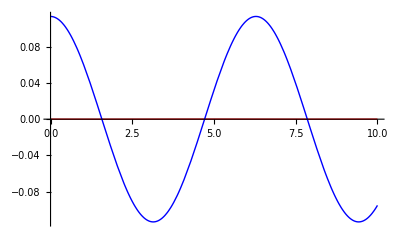

```mathematica
(* High c *)
parameters={m-> 1,l1->1,l2->1, g->981/100, Τ0->1, wf->1,c->10000};
ypplot = yp /.parameters;
Plot[ypplot, {t,0,10}, PlotStyle->{Red, Blue}]
```

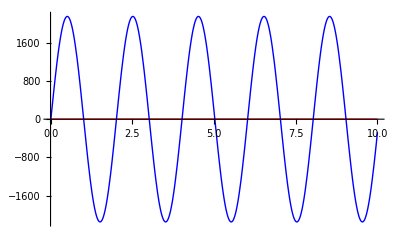

{-2146.86,{t→-0.491093}}

```mathematica
(* High c *)
parameters={m-> 1,l1->1,l2->1, g->981/100, Τ0->3.3, wf->3.1321,c->10000};
ypplot = yp /.parameters;
Plot[ypplot, {t,0,10}, PlotStyle->{Red, Blue}]
FindMinimum[ypplot[[2]], {t, .1}]
```

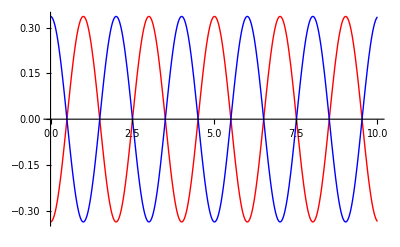

{-0.336393,{t→1.00303}}

```mathematica
(* Low c. Note the MUCH smaller displacement for the second pendulum. *)
parameters={m-> 1,l1->1,l2->1, g->981/100, Τ0->3.3, wf->3.1321,c->0};
ypplot = yp /.parameters;
Plot[ypplot, {t,0,10}, PlotStyle->{Red, Blue}]
FindMinimum[ypplot[[2]], {t, .1}]
```

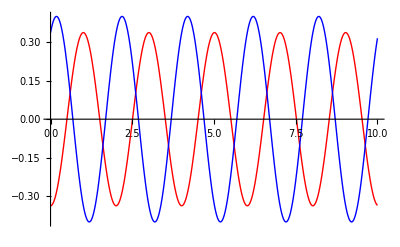

{-0.399124,{t→-0.821593}}

```mathematica
(* With c -> 1, linearization becomes invalid (assuming a cutoff displacement of .4 radians) when Τ0 = 3.3 N m and wf = 3.1321 radians/second. *)
parameters={m-> 1,l1->1,l2->1, g->981/100, Τ0->3.3, wf->3.1321,c->1};
ypplot = yp /.parameters;
Plot[ypplot, {t,0,10}, PlotStyle->{Red, Blue}]
FindMinimum[ypplot[[2]], {t, .1}]
```